# Smooth code for ISO

```mathematica
Clear["Global`*"]
```

```mathematica
param={v01->1.5,v02->2,delta1->0,delta2->0,epsilon1->0,epsilon2->0,alfa->4,dz->2}
```

{v01→1.5,v02→2,delta1→0,delta2→0,epsilon1→0,epsilon2→0,alfa→4,dz→2}

```mathematica
z0=3
```

3

## m1 smoothing

## unsmooth model for m1

## smoothed model

```mathematica
a=1/v01/.param;
```

```mathematica
b=1/v02/.param;
```

```mathematica
K=Piecewise[{{a,x≤z0},{b,x≥z0}}]
```

Piecewise[{{0.666667, x≤3}, {1/2, x≥3}, {0, True}}]

```mathematica
m1:=a/;x≤z0;
```

```mathematica
m1:=b/;x≥z0;
```

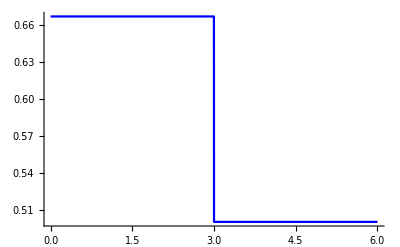

```mathematica
L1=Plot[m1,{x,0,6},PlotStyle->Blue,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
F1=(Integrate[K*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
S1=N[Integrate[a-F1,{z,z0-dz/2/.param,z0}]];
```

```mathematica
S2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
A1=N[S1/S2];
```

```mathematica
M1=F1-A1*E^(-alfa*(z-z0-dz)^2)+A1*E^(-alfa*(z+dz-z0)^2)/.param;
```

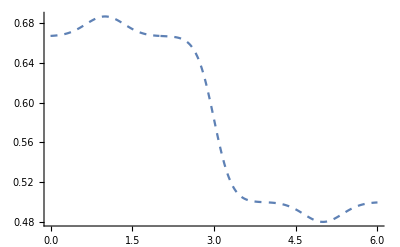

```mathematica
L2=Plot[M1,{z,0,6},PlotStyle->Dashed,AxesOrigin->{0,0.3},PlotRange->All]
```

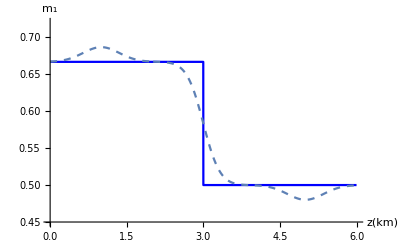

```mathematica
Show[{L1,L2},AxesOrigin->{0,0.45},PlotRange->{{0,6},{0.45,0.72}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_1",FontSize->15]}]
```

```mathematica
(*HeavisideTheta*)
```

## m2 smoothing

## smoothed model

```mathematica
a1=v01*(1+2*delta1)/.param;
```

```mathematica
b1=v02*(1+2*delta2)/.param;
```

```mathematica
K1=Piecewise[{{a1,x≤z0},{b1,x≥z0}}]
```

Piecewise[{{1.5, x≤3}, {2, x≥3}, {0, True}}]

## unsmooth model for V0

```mathematica
m2:=a1/;x≤z0;
```

```mathematica
m2:=b1/;x≥z0;
```

```mathematica
Ln1=Plot[m2,{x,0,6},PlotStyle->Blue,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Fn1=(Integrate[K1*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Sn1=N[Integrate[Fn1-a1,{z,z0-dz/2/.param,z0}]];
```

```mathematica
Sn2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
An1=N[Sn1/Sn2]
```

0.0597535

```mathematica
M2=Fn1-An1*E^(-alfa*(z+dz-z0)^2)+An1*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
Ln2=Plot[M2,{z,0,6},PlotStyle->Dashed,AxesOrigin->{0,0},PlotRange->All];
```

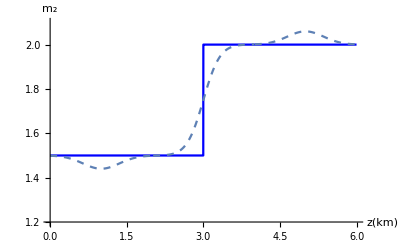

```mathematica
Show[{Ln1,Ln2},AxesOrigin->{0,1.2},PlotRange->{{0,6},{1.2,2.1}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_2",FontSize->15]}]
```

## eta smoothing

## composite param

```mathematica
a2=v01^3*(1+2*delta1)*(1+8*epsilon1-6*delta1)/.param;
```

```mathematica
b2=v02^3*(1+2*delta2)*(1+8*epsilon2-6*delta2)/.param;
```

```mathematica
K2=Piecewise[{{a2,x≤z0},{b2,x≥z0}}]
```

Piecewise[{{3.375, x≤3}, {8, x≥3}, {0, True}}]

## unsmooth model for m3

```mathematica
m3:=a2/;x≤z0;
```

```mathematica
m3:=b2/;x≥z0;
```

```mathematica
L1e=Plot[m3,{x,0,6},PlotStyle->Blue,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Fn1e=(Integrate[K2*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Sn1e=N[Integrate[Fn1e-a2,{z,z0-dz/2/.param,z0}]];
```

```mathematica
Sn2e=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-dz/2,z0+dz/2}]/.param];
```

```mathematica
An1e=N[Sn1e/Sn2e];
```

```mathematica
M3=Fn1e-An1e*E^(-alfa*(z+dz-z0)^2)+An1e*E^(-alfa*(z-dz-z0)^2)/.param;
```

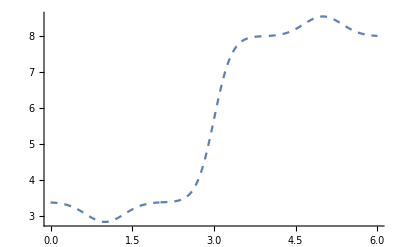

```mathematica
Ln2e=Plot[M3,{z,0,6},PlotStyle->Dashed,AxesOrigin->{0,0},PlotRange->All]
```

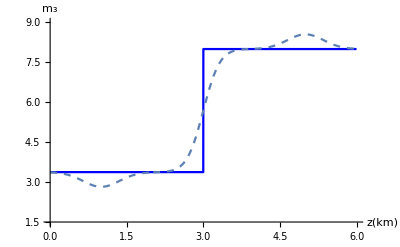

```mathematica
Show[{L1e,Ln2e},AxesOrigin->{0,1.5},PlotRange->{{0,6},{1.5,9}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_3",FontSize->15]}]
```

## convert to the model parameters

```mathematica
V0=1/M1;
```

```mathematica
DELTA=(M1*M2-1)/2;
```

```mathematica
EPSILON=(((M3*M1^2)/M2)+3*M1*M2-4)/8;
```

## unsmoothed model parameters

```mathematica
vel1:=v01/;x≤z0;
```

```mathematica
vel1:=v02/;x≥z0;
```

```mathematica
p10=Plot[vel1/.param,{x,0,6},PlotStyle->Blue,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p1=Plot[V0,{z,0,6},PlotStyle->Dashed,AxesOrigin->{0,0},PlotRange->All];
```

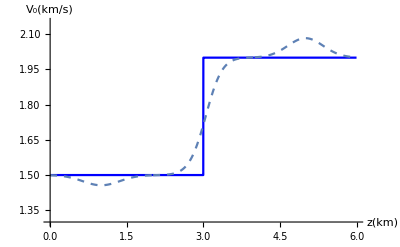

```mathematica
Show[{p10,p1},AxesOrigin->{0,1.3},PlotRange->{{0,6},{1.3,2.15}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_0(km/s)",FontSize->15]}]
```

```mathematica
De1:=delta1/;x≤z0;
```

```mathematica
De1:=delta2/;x≥z0;
```

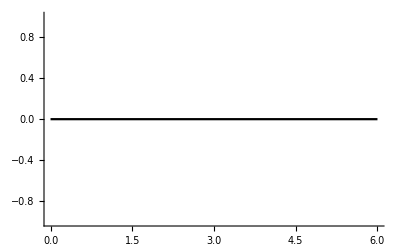

```mathematica
p20=Plot[De1/.param,{x,0,6},PlotStyle->Black,AxesOrigin->{0,-2},PlotRange->All]
```

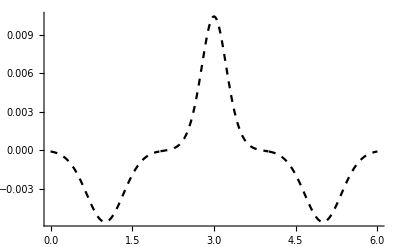

```mathematica
p2=Plot[DELTA,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,-0.1},PlotRange->All]
```

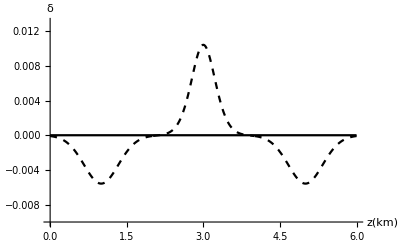

```mathematica
Show[{p20,p2},AxesOrigin->{0,-0.01},PlotRange->{{0,6},{-0.01,0.013}},AxesLabel->{Style["z(km)",FontSize->15],Style["δ",FontSize->15]}]
```

```mathematica
EPS1:=epsilon1/;x≤z0;
```

```mathematica
EPS1:=epsilon2/;x≥z0;
```

```mathematica
p30=Plot[EPS1/.param,{x,0,6},PlotStyle->Black,PlotRange->All];
```

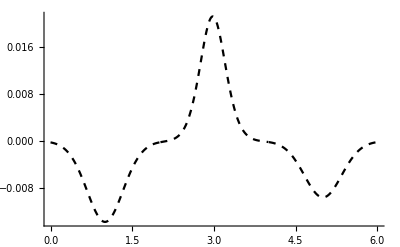

```mathematica
p3=Plot[EPSILON,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,-0.05},PlotRange->All]
```

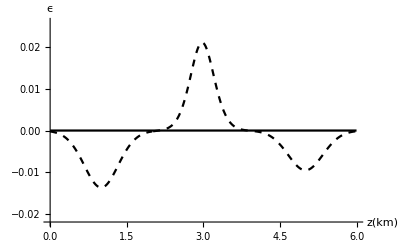

```mathematica
Show[{p30,p3},AxesOrigin->{0,-0.022},PlotRange->{{0,6},{-0.022,0.026}},AxesLabel->{Style["z(km)",FontSize->15],Style["ϵ",FontSize->15]}]
```

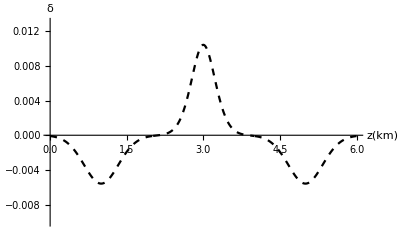

```mathematica
Show[{p2},AxesOrigin->{0,0},PlotRange->{{0,6},{-0.01,0.013}},AxesLabel->{Style["z(km)",FontSize->15],Style["δ",FontSize->15]}]
```

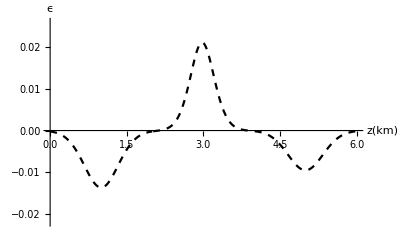

```mathematica
Show[{p3},AxesOrigin->{0,0},PlotRange->{{0,6},{-0.022,0.026}},AxesLabel->{Style["z(km)",FontSize->15],Style["ϵ",FontSize->15]}]
```